## Independence of functional forms

### Intrinsic growth rates - Second power

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^2/ω^2-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^2/ω^2-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→1-(S-ϵ)^2/ω^2},{N_1→(-S^2 (-1+α)+2 S α ϵ-α ϵ^2+(-1+α) ω^2)/((-1+α^2) ω^2),N_2→(-S^2 (-1+α)-2 S ϵ+ϵ^2+(-1+α) ω^2)/((-1+α^2) ω^2)},{N_1→1-S^2/ω^2,N_2→0}}

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[1.8,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3156,0,198,0,0}

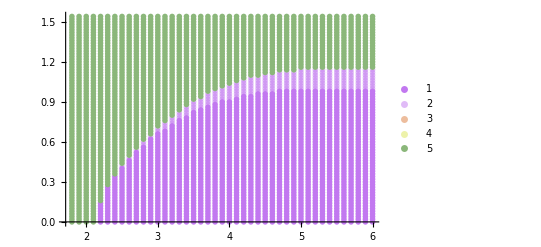

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

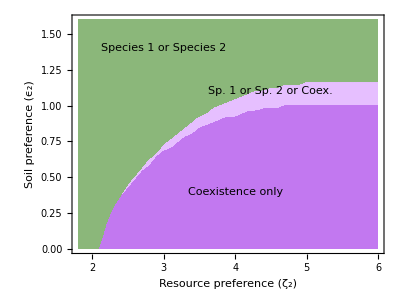

```mathematica
figS1a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.8,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS1a.pdf",figS1a];
```

### Intrinsic growth rates - Fourth power

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→1-(S-ϵ)^4/ω^4},{N_1→(-S^4 (-1+α)+4 S^3 α ϵ-6 S^2 α ϵ^2+4 S α ϵ^3-α ϵ^4+(-1+α) ω^4)/((-1+α^2) ω^4),N_2→(-S^4 (-1+α)-4 S^3 ϵ+6 S^2 ϵ^2-4 S ϵ^3+ϵ^4+(-1+α) ω^4)/((-1+α^2) ω^4)},{N_1→1-S^4/ω^4,N_2→0}}

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[1.8,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2831,0,523,0,0}

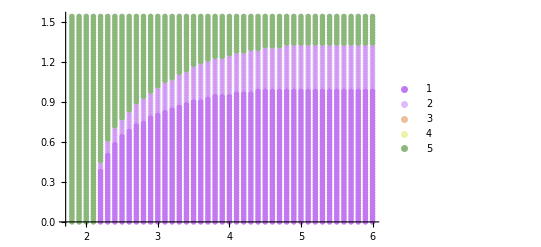

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

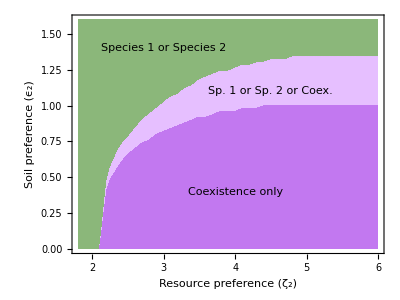

```mathematica
figS1b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.8,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS1b.pdf",figS1b];
```

### Intrinsic growth rates - Eighth power

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^8/ω^8-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^8/ω^8-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[1.8,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2455,0,899,0,0}

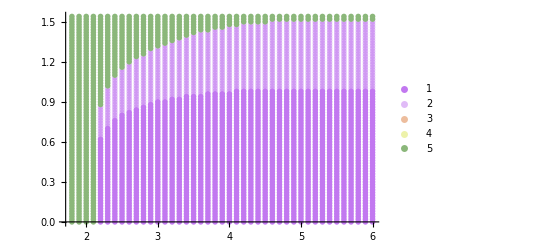

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

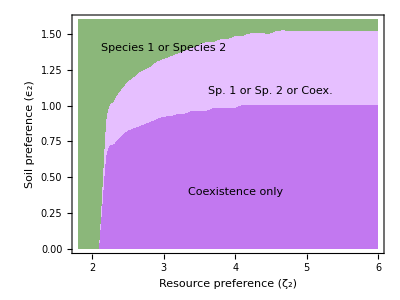

```mathematica
figS1c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,1.8,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS1c.pdf",figS1c];
```

### Competition coefficient - Narrow total utilization curve δ=1

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/σ^4],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,3908,0,850,0,0}

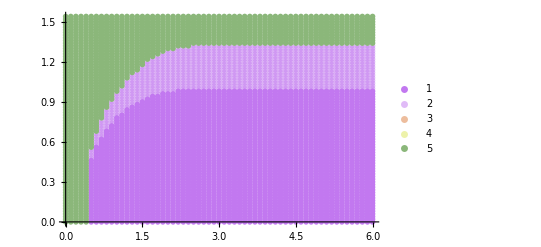

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

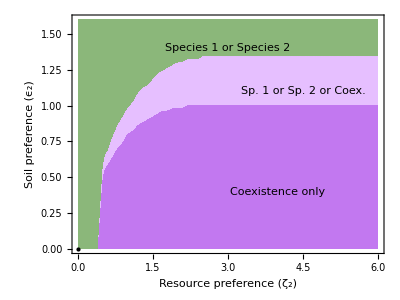

```mathematica
figS2a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS2a.pdf",figS2a];
```

### Competition coefficient - Intermediate total utilization curve δ=2

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(16 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,4076,0,682,0,0}

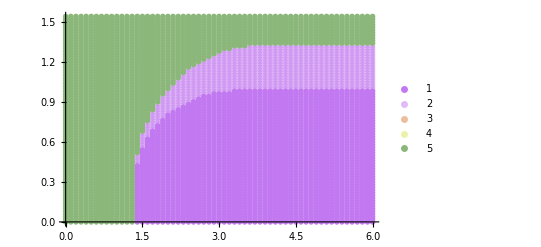

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

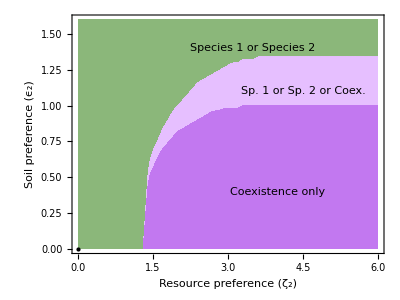

```mathematica
figS2b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{{PointSize[Large],Point[{0,0}]},Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS2b.pdf",figS2b];
```

### Competition coefficient - Wide total utilization curve δ=3

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.54,0.02];
nϵ=Length[ϵs];
ζs=Range[0,6,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=f[ν/.pars,σ/.pars,ζs[[j1]]];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,4235,0,523,0,0}

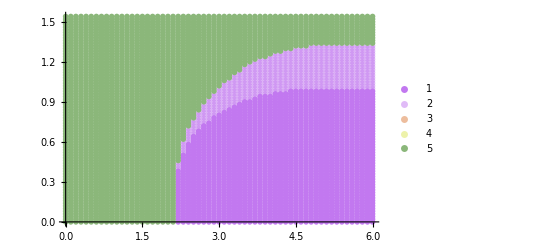

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

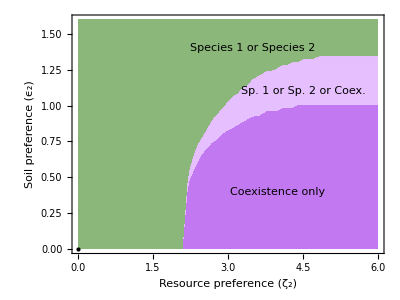

```mathematica
figS2c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,6},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{3.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{4.5,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{4,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS2c.pdf",figS2c];
```

### Competition coefficient - Quadratic total utilization ~ Quadratic function of trait difference

#### Setup

```mathematica
ClearAll["α","f"]
```

```mathematica
ν Integrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^2)/σ^2],{x,-Infinity,Infinity},Assumptions->σ>0]/Integrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity},Assumptions->σ>0]
```

ⅇ^(-ζ^2/(2 σ^2)) ν

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ^2/(2 σ^2)];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2594,0,522,0,0}

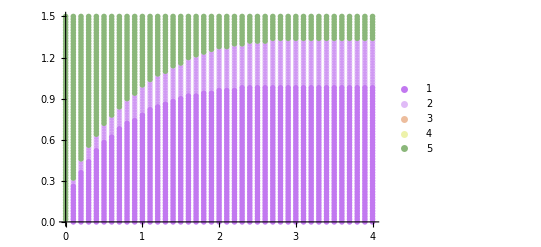

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

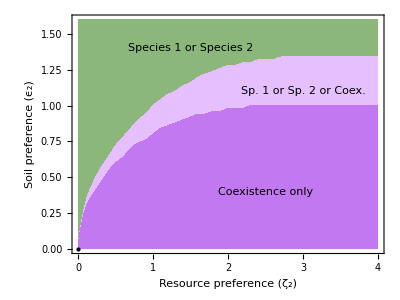

```mathematica
figS3b=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS3b.pdf",figS3b];
```

### Competition coefficient - Absolute value of trait difference

```mathematica
ClearAll["α","f"]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ/(2σ)];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2652,0,464,0,0}

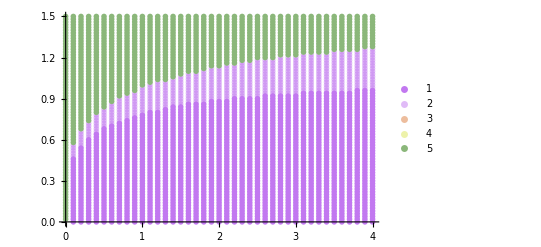

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

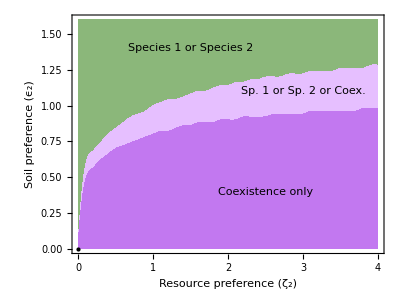

```mathematica
figS3a=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS3a.pdf",figS3a];
```

### Competition coefficient - Quartic function of trait difference

```mathematica
ClearAll["α","f"]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Phase space

```mathematica
pars={ω->1,σ->1,ν->1,η->1};
ϵs=Range[0,1.5,0.02];
nϵ=Length[ϵs];
ζs=Range[0,4,0.1];
nζ=Length[ζs];
```

```mathematica
eq=Array[,{nζ,nϵ}];
λ1=Array[,{nζ,nϵ}];
λ2=Array[,{nζ,nϵ}];
λ3=Array[,{nζ,nϵ}];
z1=Array[,{nζ,2}];
z2=Array[,{nζ,2}];
z3=Array[,{nζ,2}];
z4=Array[,{nζ,2}];
z5=Array[,{nζ,2}];
z6=Array[,{nζ,2}];
y1=Array[,{nϵ*nζ,2}];
y2=Array[,{nϵ*nζ,2}];
y3=Array[,{nϵ*nζ,2}];
y4=Array[,{nϵ*nζ,2}];
y5=Array[,{nϵ*nζ,2}];
```

```mathematica
eqCounts=List[0,0,0,0,0,0];
```

```mathematica
Do[
ch1=0;
ch2=0;
Do[
α=ν Exp[-ζ^4/(2 σ^4)];
eq[[j1,j2]]=FullSimplify[Solve[(Subscript[dN, 1]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(Subscript[dN, 2]/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]])==0&&(dS/.pars/.ϵ->ϵs[[j2]])==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]];
If[Length[eq[[j1,j2]]]==3,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2,2]]]]];
If[Length[eq[[j1,j2]]]==1,
λ1[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.eq[[j1,j2]]]]];
λ2[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->1,Subscript[N, 2]->0,S->0}]];
λ3[[j1,j2]]=Max[Eigenvalues[Jc/.pars/.ϵ->ϵs[[j2]]/.ζ->ζs[[j1]]/.{Subscript[N, 1]->0,Subscript[N, 2]->1,S->ϵs[[j2]]}]];

eqCounts[[Length[eq[[j1,j2]]]+1]]++;

If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]≥0&& λ3[[j1,j2]]≥0,y1[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[λ1[[j1,j2]]<0&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y2[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]≥0,y3[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]>=0&& λ3[[j1,j2]]<0,y4[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];
If[(λ1[[j1,j2]]≥0||λ1[[j1,j2]]==Null[j1,j2])&& λ2[[j1,j2]]<0&& λ3[[j1,j2]]<0,y5[[(j1-1)*nϵ+j2]]={ζs[[j1]],ϵs[[j2]]}];

If[λ2[[j1,j2]]<0&&ch1==0,z1[[j1]]={ζs[[j1]],ϵs[[j2]]};ch1=1];
If[(λ1[[j1,j2]]>=0||λ1[[j1,j2]]==Null[j1,j2])&&λ2[[j1,j2]]<0&&λ3[[j1,j2]]<0&&ch2==0,z2[[j1]]={ζs[[j1]],ϵs[[j2]]};ch2=1],

{j2,nϵ}],
{j1,nζ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

1 - coex only
2 - coex + s1 + s2
3 - s1
4 - s2
5 - s1 + s2 (priority effect)

```mathematica
eqCounts
```

{0,2579,0,537,0,0}

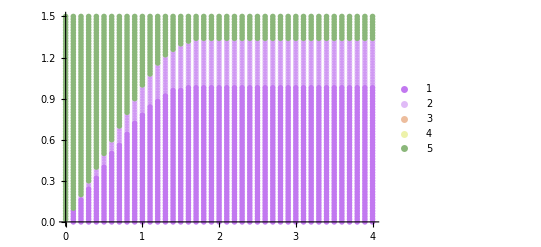

```mathematica
ListPlot[{y1,y2,y3,y4,y5},PlotLegends->Automatic,PlotMarkers->{•,8},PlotStyle->{{ColorData["Pastel",0]},{ColorData["Pastel",0],Opacity[0.5]},{ColorData["Pastel",1/3]},{ColorData["Pastel",2/3]},{ColorData[95,0]}}]
```

```mathematica
f1=Interpolation[z1];
f2=Interpolation[z2];
```

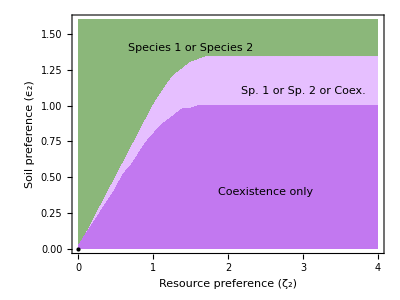

```mathematica
figS3c=RegionPlot[{y>f2[x],y<f2[x],y<f1[x]},{x,0,4},{y,0,1.6},PlotStyle->{{ColorData[95,0],Opacity[1]},{RGBColor[0.9,0.75,1,0.99]},{ColorData["Pastel",0],Opacity[1]}},BoundaryStyle->None,Frame->True,FrameLabel->{"Resource preference (ζ_2)","Soil preference (ϵ_2)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},Epilog-> {{PointSize[Large],Point[{0,0}]},{Inset[Text[Style["Species 1 or Species 2",FontSize->13]],{1.5,1.4}],Inset[Text[Style["Sp. 1 or Sp. 2 or Coex. ",FontSize->13]],{3,1.1}],Inset[Text[Style["Coexistence only ",FontSize->13]],{2.5,0.4}]}},AspectRatio->0.75]
```

```mathematica
Export["\\\\wsl.localhost\\Debian\\home\\athma\\trait_cond_models\\paper_2\\images\\figS3c.pdf",figS3c];
```

## Numerics

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->0.5,ϵ->1.3};
```

```mathematica
α=ν Exp[-ζ^4/(2 σ^4)]/.pars
```

0.969233

```mathematica
x0=0.1;y0=0.1;z0=0.5; T=100; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

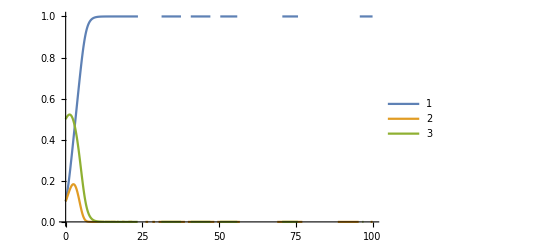

```mathematica
Plot[{x[t]/.nsol,y[t]/.nsol,z[t]/.nsol},{t,0,100},PlotRange->{0,1},PlotLegends->Automatic]
```

```mathematica
eqNSol=FullSimplify[Solve[N[Subscript[dN, 1]/.pars]==0&&N[Subscript[dN, 2]/.pars]==0&&N[dS/.pars]==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→0.417164,N_2→0.417164,S→0.65}}

```mathematica
Eigenvalues[Jc/.pars/.eqNSol[[1]]]
```

{-1.29791,-0.662611,0.450743}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->1/.Subscript[N, 2]->0/.S->0]
```

{-2.6349,-1.,-1.}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->0/.Subscript[N, 2]->1/.S->1.3]
```

{-2.6349,-1.,-1.}